```mathematica
imgsize=700;
```

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/GitHub/NeuPhysics/codebase/mma/matter

```mathematica
thetamV=Pi/5;
k1V=0.3;
k2V=0.7;
a1V=0.1(k1V)^(-5/3);
a2V=0.1(k1V)^(-5/3);
phi1V=0;
phi2V=0;
```

```mathematica
bCoef[n1_,n2_,k1_,k2_,a1_,a2_]:=-(-I)^(n1+n2)Tan[2thetamV]/2 n1 k1 BesselJ[n1,a1/k1 Cos[2thetamV]]BesselJ[n2,a2/k2 Cos[2thetamV]]
```

```mathematica
coefDenPlt[k1_,k2_,a1_,a2_,range_]:=Module[{n1M,n2M,k1M,k2M,a1M,a2M,coeffList,coeffListRe,coeffListIm,coeffListAbs,list1,list2,list3,list4,n2List1,n1List2,n2List3,n1List4,meshStyle},
meshStyle=None;
k1M=k1;
k2M=k2;
a1M=a1;
a2M=a2;
coeffList=Flatten[Table[{n1,n2,bCoef[n1,n2,k1M,k2M,a1M,a2M]+bCoef[n2,n1,k2M,k1M,a2M,a1M]},{n1,-range,range},{n2,-range,range}],1];
coeffListRe=Flatten[Table[{n1,n2,Log@Re[bCoef[n1,n2,k1M,k2M,a1M,a2M]+bCoef[n2,n1,k2M,k1M,a2M,a1M]]},{n1,-range,range},{n2,-range,range}],1];
coeffListIm=Flatten[Table[{n1,n2,Log@Im[bCoef[n1,n2,k1M,k2M,a1M,a2M]+bCoef[n2,n1,k2M,k1M,a2M,a1M]]},{n1,-range,range},{n2,-range,range}],1];
coeffListAbs=Flatten[Table[{n1,n2,Log@Abs[bCoef[n1,n2,k1M,k2M,a1M,a2M]+bCoef[n2,n1,k2M,k1M,a2M,a1M]]},{n1,-range,range},{n2,-range,range}],1];
n2List1=0;
list1=Table[{n1,Abs[bCoef[n1,n2List1,k1M,k2M,a1M,a2M]+bCoef[n2List1,n1,k2M,k1M,a2M,a1M]]},{n1,-range,range}];
n1List2=0;
list2=Table[{n2,Abs[bCoef[n1List2,n2,k1M,k2M,a1M,a2M]+bCoef[n2,n1List2,k2M,k1M,a2M,a1M]]},{n2,-range,range}];
n2List3=Round[range/2];
list3=Table[{n1,Abs[bCoef[n1,n2List3,k1M,k2M,a1M,a2M]+bCoef[n2List3,n1,k2M,k1M,a2M,a1M]]},{n1,-range,range}];
n1List4=Round[range/2];
list4=Table[{n2,Abs[bCoef[n1List4,n2,k1M,k2M,a1M,a2M]+bCoef[n2,n1List4,k2M,k1M,a2M,a1M]]},{n2,-range,range}];
Grid[{{Grid[{{Text["Parameters:\n k1="<>ToString[k1M]<>";\n k2="<>ToString[k2M]<>";\n a1="<>ToString[a1M]<>";\n a2="<>ToString[a2M]<>";\n\n"]},{ListLogPlot[{list1,list2,list3,list4},ImageSize->imgsize,Frame->True,PlotLabel->"Slicings",Joined->True,PlotLegends->Placed[{"n2="<>ToString[n2List1],"n1="<>ToString[n1List2],"n2="<>ToString[n2List3],"n1="<>ToString[n1List4]},{Top,Center}]]}}],ListDensityPlot[coeffListAbs,Mesh->meshStyle,FrameLabel->{"n1","n2"},ColorFunction->"AvocadoColors",PlotLegends->All,ImageSize->imgsize,PlotLabel->"Absolute Value of The Coefficient"]},{ListDensityPlot[coeffListRe,Mesh->meshStyle,FrameLabel->{"n1","n2"},ColorFunction->"AvocadoColors",PlotLegends->All,ImageSize->imgsize,PlotLabel->"Real Part of The Coefficient"],ListDensityPlot[coeffListIm,Mesh->meshStyle,FrameLabel->{"n1","n2"},ColorFunction->"AvocadoColors",PlotLegends->All,ImageSize->imgsize,PlotLabel->"Imaginary Part of The Coefficient"]}}]
]
```

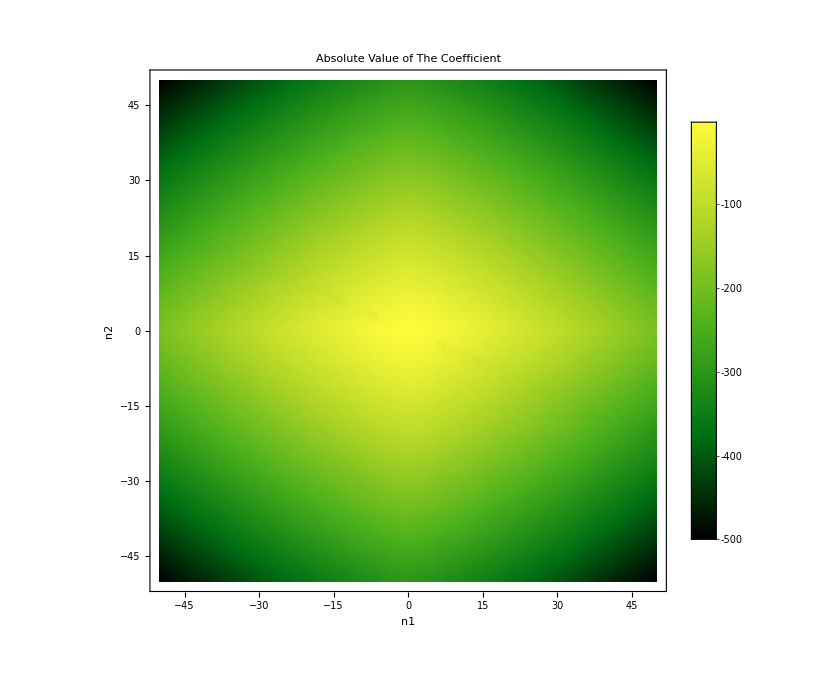
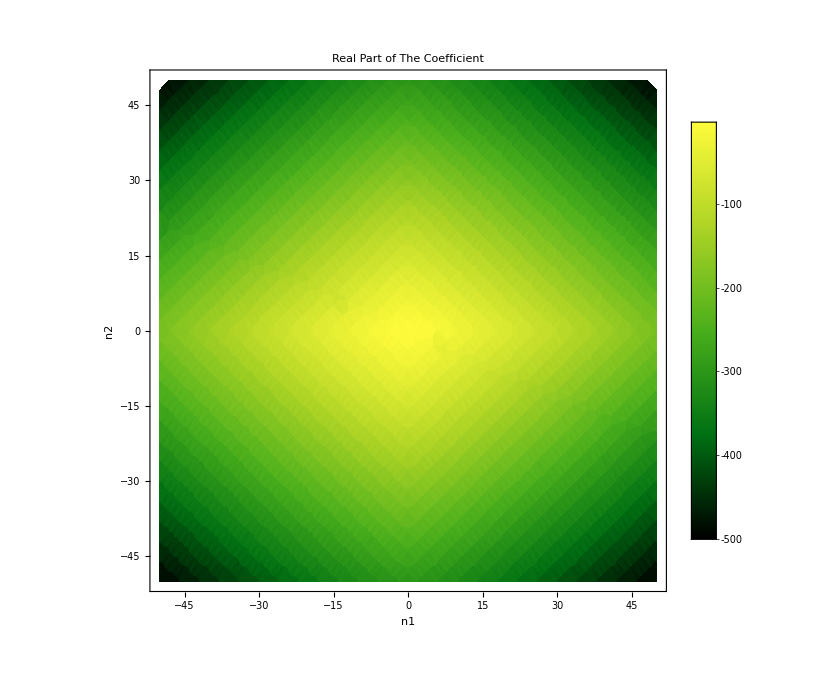
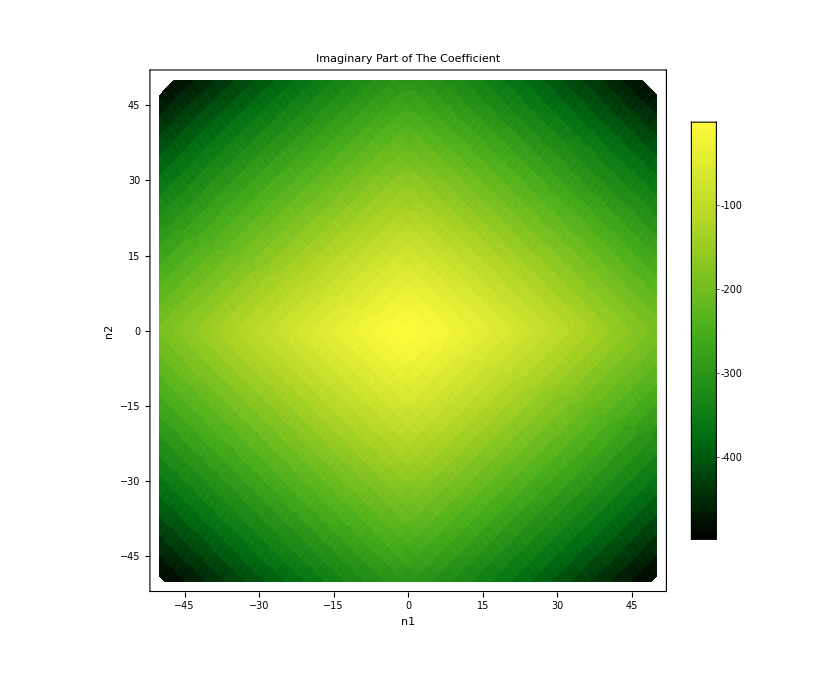
Parameters:
 k1=0.3;
 k2=0.7;
 a1=0.743814;
 a2=0.181205;


-Graphics- | -Graphics-
-Graphics- | -Graphics-

export/stimulated-2-freq-coef-non-approx-a2-larger-non-mesh.png

```mathematica
Module[{},
k1A=k1V;
k2A=k2V;
a1A=0.1(k1V)^(-5/3);
a2A=0.1(k2V)^(-5/3);
coefDenPlt[k1A,k2A,a1A,a2A,50]
]
Export["export/stimulated-2-freq-coef-non-approx-a2-larger-non-mesh.png",%]
```

```mathematica
Manipulate[ListDensityPlot[Flatten[Table[{n1,n2,Log@Abs[bCoef[n1,n2,k1Mani,k2Mani,0.1(k1Mani)^(-5/3),0.1(k2Mani)^(-5/3)]+bCoef[n2,n1,k2Mani,k1Mani,0.1(k2Mani)^(-5/3),0.1(k1Mani)^(-5/3)]]},{n1,-range,range},{n2,-range,range}],1],Mesh->All,FrameLabel->{"n1","n2"},ColorFunction->"AvocadoColors",PlotLegends->Automatic,ImageSize->imgsize],{k1Mani,0.1,2},{k2Mani,0.1,2}]
```

```mathematica
Grid[{{ Grid[{{A},{F}}] ,B},{C,D}}]
```

A
F | B
C | D